```mathematica
Etlambda[lamda_, q_] := q/(1000 - lamda * q) + ((1-q)/(1000 - (1-q)*lamda))*(1 - (1-q) * lamda * 296/ (300*2000))
lambda = 600;
q/.FindMinimum[{Etlambda[lambda,q], 0 <= q <= 1}, {q, 0}][[2]]
```

0.399737

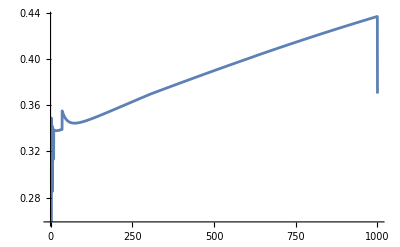

```mathematica
lmdaMin = 0;
lmdaMax = 1000;
Plot[q /.FindMinimum[{Etlambda[lmda,q], 0 <= q <= 1}, {q, 0}][[2]], {lmda, lmdaMin, lmdaMax}]
```

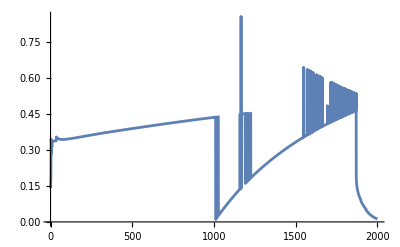

```mathematica
lmdaMax = 2000;
Plot[q /.FindMinimum[{Etlambda[lmda,q], 0 <= q <= 1}, {q, 0}][[2]], {lmda, lmdaMin, lmdaMax}]
```